DIRECTIONS FOR THE PROBLEM SET

Do Problems 1 and 3 before class.

We are going to work through Problem 2 in class together. You don’t need to do anything on Problem 2 prior to class.

Together, in class, we will act like a big, randomized server farm and get about 200 samples of the probability distribution.

If we are all careful, we’ll start to see the pattern emerge. When I started in bin 2, my algorithm stayed on bin 2 so much of the time the pattern had not really emerged. But I only got 20 samples.

## Bayesian Statistics, Assignment for Friday, Dec. 6

## Reading

For Tuesday, Dec. 3, I had you read Donovan and Mickey Chapter 15 to p 235. I’d just like you to re-read the material to p. 229. You are of course welcome to do Donovan and Mickey’s tedious example that starts on p. 235, but we’ll be doing my example, so I don’t think you need to.

Donovan and Mickey are doing all of their Chapter 15 development for a continuous distribution. They have a distribution P(p) that we are sampling, and sometimes they call it P(θ). So they are already doing the continuous case. I am trying to bring the discussion down to earth by going back to a problem with discrete bins. I am going back to the problem of sampling the iPhone quarterly sales distribution.

## For Problem Set 17 — Illustrating Metropolis-Hastings

When we last looked at the iPhone quarterly sales distribution, I made the odd assumption that if you move right from bin Q4 you get to bin Q1. And similarly, if you move left from bin Q1 you get to bin Q4.

The odd assumptions were to create a distribution without edges.  The absence of edges allowed us to have a perfectly symmetric chance of proposing to go left or right  from the current bin. 

In this problem set we will be forced to have an asymmetrical chance of proposing to go left or right.

However, the distribution we are going to sample is exactly the same, just without the edges. Here are the slightly hokey sales figures:

```mathematica
unitSalesByQuarter = {
{"Q1", 25000000},
{"Q2", 50000000},
{"Q3", 100000000},
{"Q4", 75000000}
};
annualUnitSales = Total[unitSalesByQuarter[[All,2]]];
```

We can normalize the sales figure to the total sales, so that the sum of all the bars is 1.0 rather than 250,000,000.

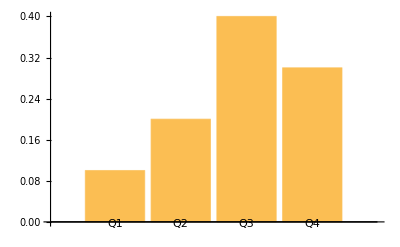

```mathematica
normalizedUnitSales = N[unitSalesByQuarter[[All,2]]/= annualUnitSales];
BarChart[normalizedUnitSales,ChartLabels->unitSalesByQuarter[[All,1]]]
```

Not only am I no longer going to have the unusual wrapping behavior, I am going to change something else:

We used to simply flip a coin to decide whether to go left or right. Now we are instead going to roll a six-sided die, and there will be four outcomes based on the six possibilities as follows:

If the die shows 1, we go two bins to the left. So that is 1/6 of the time.
If the die shows 2 or 3, we go one bin to the left. So that is 1/3 of the time.
If the die shows 4 or 5, we go one bin to the right. So that is 1/3 of the time.
If the die shows 6, we go two bins to the right. So that is 1/6 of the time.

But what about the edges!! The above rules can’t hold! We have to harmonize these outcomes with these constraints:

From bin Q4 we cannot go to the right.
From bin Q3, we can go to the right but not by two bins.
From bin Q2, we can go to the left, but not by two bins.
From bin Q1 we cannot go to the left.

The question is, how do we harmonize the constraints with what the die shows?!?

NOTE: We are in part of the algorithm where we are deciding what movements to propose. The probability of accepting a proposal comes later.

Well, how about if you get an illegal movement, you ignore the movement and roll again? Here is the resulting set of movements and their probabilities that using this procedure would give:

proposing Q1->Q2:g(2|1)=2/3 (one-bin move)
proposing Q1->Q3:g(3|1)=1/3 (two-bin move)

proposing Q2->Q1:g(1|2)=2/5 (one-bin move)
proposing Q2->Q3:g(3|2)=2/5 (one-bin move)
proposing Q2->Q4:g(4|2)=1/5 (two-bin move)

proposing Q3->Q1:g(1|3)=1/5 (two-bin move)
proposing Q3->Q2:g(2|3)=2/5 (one-bin move)
proposing Q3->Q4:g(4|3)=2/5 (one-bin move)

proposing Q4->Q3:g(3|4)=2/3 (one-bin move)
proposing Q4->Q2:g(2|4)=1/3 (two-bin move)

NOTE: I have used g(n_proposed|n_current) perfectly analogously to Donovan and Mickey p. 229.

### Problem 1 — Compute the probabilities for accepting the movements.

Now I want you to compute the probabilities of accepting each of the 10 movements. I did the first one for you. You need the g(n_proposed|n_current) tabulated above. For convenience, I will recopy the other numbers you need: p_1=0.1, p_2=0.2, p_3=0.4, p_4=0.3.
 
accepting Q1->Q2:p_2/(p_1+p_2)(g(1|2))/(g(2|1))=0.2/(0.1+0.2)(2/5)/(2/3)=2/3·3/5=2/5=0.40 (two decimal places is good)
accepting Q1->Q3:p_3/(p_1+p_3)(g(1|3))/(g(3|1))=
 
accepting Q2->Q1:p_1/(p_1+p_2)(g(2|1))/(g(1|2))=
accepting Q2->Q3:p_3/(p_2+p_3)(g(2|3))/(g(3|2))=
accepting Q2->Q4:p_4/(p_2+p_4)(g(2|4))/(g(4|2))=
 
accepting Q3-> Q1:p_1/(p_1+p_3)(g(3|1))/(g(1|3))=
accepting Q3->Q2:p_2/(p_2+p_3)(g(3|2))/(g(2|3))=
accepting Q3->Q4:p_4/(p_3+p_4)(g(3|4))/(g(4|3))=
 
accepting Q4-> Q3:p_3/(p_3+p_4)(g(4|3))/(g(3|4))=
accepting Q4->Q2:p_2/(p_2+p_4)(g(4|2))/(g(2|4))=

## Problem 2 — Let’s Do Metropolis-Hastings

```mathematica
smallIterations=31;
randomReals=Round[RandomReal[{0,1},smallIterations],0.01];
randomDieTosses=RandomInteger[{1,6},smallIterations];
rounds=Range[1,smallIterations];
blanks = ConstantArray["                  ",smallIterations];
TableForm[Transpose[{rounds,blanks, randomDieTosses, blanks, randomReals, blanks}], TableHeadings->{{},{"round", "current bin", "die", "proposed bin","random", "result bin"}}]
```

| round | current bin | die | proposed bin | random | result bin
 | 1 |                    | 6 |                    | 0.5 |                   
 | 2 |                    | 5 |                    | 0.26 |                   
 | 3 |                    | 3 |                    | 0.19 |                   
 | 4 |                    | 1 |                    | 0.59 |                   
 | 5 |                    | 1 |                    | 0.91 |                   
 | 6 |                    | 1 |                    | 0.35 |                   
 | 7 |                    | 5 |                    | 0.13 |                   
 | 8 |                    | 2 |                    | 0.82 |                   
 | 9 |                    | 1 |                    | 0.84 |                   
 | 10 |                    | 5 |                    | 0.84 |                   
 | 11 |                    | 3 |                    | 0.46 |                   
 | 12 |                    | 3 |                    | 0.37 |                   
 | 13 |                    | 2 |                    | 0.97 |                   
 | 14 |                    | 5 |                    | 0.19 |                   
 | 15 |                    | 2 |                    | 0.79 |                   
 | 16 |                    | 4 |                    | 0.22 |                   
 | 17 |                    | 5 |                    | 0.99 |                   
 | 18 |                    | 6 |                    | 0.99 |                   
 | 19 |                    | 2 |                    | 0.49 |                   
 | 20 |                    | 2 |                    | 0.11 |                   
 | 21 |                    | 2 |                    | 0.2 |                   
 | 22 |                    | 5 |                    | 0.83 |                   
 | 23 |                    | 2 |                    | 0.18 |                   
 | 24 |                    | 3 |                    | 0.22 |                   
 | 25 |                    | 5 |                    | 0.68 |                   
 | 26 |                    | 1 |                    | 0.69 |                   
 | 27 |                    | 1 |                    | 0.44 |                   
 | 28 |                    | 4 |                    | 0.9 |                   
 | 29 |                    | 6 |                    | 0.54 |                   
 | 30 |                    | 3 |                    | 0.64 |                   
 | 31 |                    | 3 |                    | 0.48 |

Choose a bin at random to start. Make a tally on the facing page for the initial bin.

Choose a “round” in the table to start. Make that random. On the last problem set, I had you start on your birthday. Let’s do that again. Then iterate until you get 19 more tallies. Also, if you get an illegal movement, ignore the die roll and roll again, don’t make a tally. You completely ignore iterations with an illegal movement.

I put in the birthday starting point for for two reasons: (1) It makes it harder to collaborate, and if you collaborate, you won’t learn to accurately apply the algorithm. (2) As a class, we won’t get as much independent Monte Carlo work done if any two people do the same thing. We are a server farm that will be obtaining 200 independent samples—20 from each of us.

This rest of this page left blank for making tallies and doing histograms together in class.

## 3. Where Did Things Like g(1|2)=2/5 Come From?

You might be wondering, where did I get the g(n_proposed|n_current) that you needed in Problem 1?! For example, where did I get:

proposing Q3-> Q1:g(1|3)=1/5 (two-bin move)

Go back and look at how I introduced that there will be “a six-sided die, and there will be four outcomes.” It was a tad sneaky. Pay special attention to “if you get an illegal movement, ignore the die and roll again.” I am pretty sure you make an argument by just thinking about this for a while.

To be more explicit about what I want as your answer, show me calculation I did that got me g(1|3):



Also, show me calculation I did that got me g(2|1):

## 4. Need More Challenge?

Collectively we are reaching a tremendously good place for a one-semester introduction to descriptive, frequentist, and Bayesian statistics. I will be careful not to pile too much more in the final four classes. If you want to pile some more on yourself, here are a couple of suggestions for fleshing out the theory.

A. Re-read my handout that proves that the Metropolis algorithm works. Figure out how to alter it to prove that the Metropolis-Hastings algorithm works. Your new proof is not that much different.

B. I have been using a slightly simpler ratio for deciding whether to accept the proposed move than Donovan and Mickey and everyone else uses. Prove that the Metropolis algorithm and the Metropolis-Hastings algorithm work with the slightly more complicated ratios that everybody else uses. (See Donovan and Mickey, Eqs. 15.7 and 15.8, on p. 229.)